```mathematica
FindDiagonals[g_,v1_,v2_]:=Block[{sets=Subsets[VertexList[g],{2}], notconnected, edgeList,sorted=Sort[{v1,v2}],relevantEdges},
edgeList=Map[Sort[{#[[1]],#[[2]]}]&,EdgeList[g]];
relevantEdges=Select[edgeList,Intersection[#,sorted]≠{}&];
notconnected=Select[DeleteDuplicates[Flatten[Select[sets,!MemberQ[relevantEdges,#]&]]],!MemberQ[sorted,#]&];
Print[sorted];
Print[edgeList];
Print[relevantEdges];
Print[notconnected];
Select[notconnected,MemberQ[edgeList,Sort[#,sorted[[1]]]]
&&MemberQ[edgeList,Sort[#,sorted[[2]]]]&]
]
```

```mathematica
FindDiagonals[g_,v1_,v2_]:=Block[{sets, notconnected, edgeList,notedgeList,sorted=Sort[{v1,v2}], relevantVertices},
(* just take all edges *)
edgeList=Map[Sort[{#[[1]],#[[2]]}]&,EdgeList[g]];
(* just take all edges  in the graph complement so all non-edges*)
notedgeList=Map[Sort[{#[[1]],#[[2]]}]&,EdgeList[GraphComplement[g]]];
(* relevant vertices are those connected to both v1 and v2 ....*)
relevantVertices=Select[VertexList[g],!MemberQ[sorted,#]&& MemberQ[edgeList,Sort[{#,v1}]]&& MemberQ[edgeList,Sort[{#,v2}]]&];
(* now take any combination of relevant vertices pairwise and make sure they are not connected *)
sets=Select[Map[Sort,Subsets[relevantVertices,{2}]],!MemberQ[edgeList,#]&];
sets
]
```

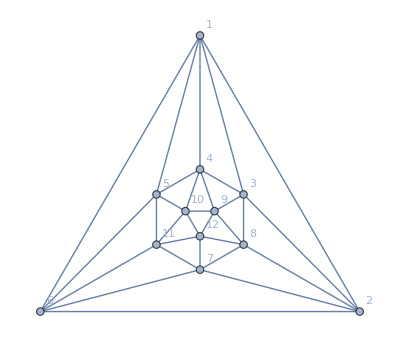

```mathematica
Graph[plantri[[1]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
FindDiagonals[Graph[plantri[[1]]],1,2]
```

{{3,6}}

```mathematica
TraverseDiag[g_]:=Block[{diag,h,chromg,edge},
chromg=ChromaticPolynomial[g,4]/24;
Table[
diag=First [FindDiagonals[g,e[[1]],e[[2]]]];
edge=UndirectedEdge[diag[[1]],diag[[2]]];
h=EdgeAdd[EdgeDelete[g,e],edge];
{e,edge,chromg,ChromaticPolynomial[h,4]/24}
,{e,EdgeList[g]}
]
]
```

```mathematica
TraverseDiag[plantri[[1]]]
```

{{1<->2,3<->6,10,12},{1<->3,2<->4,10,12},{1<->4,3<->5,10,12},{1<->5,4<->6,10,12},{1<->6,2<->5,10,12},{2<->6,1<->7,10,12},{2<->7,6<->8,10,12},{2<->8,3<->7,10,12},{2<->3,1<->8,10,12},{3<->8,2<->9,10,12},{3<->9,4<->8,10,12},{3<->4,1<->9,10,12},{4<->9,3<->10,10,12},{4<->10,5<->9,10,12},{4<->5,1<->10,10,12},{5<->10,4<->11,10,12},{5<->11,6<->10,10,12},{5<->6,1<->11,10,12},{6<->11,5<->7,10,12},{6<->7,2<->11,10,12},{7<->11,6<->12,10,12},{7<->12,8<->11,10,12},{7<->8,2<->12,10,12},{8<->12,7<->9,10,12},{8<->9,3<->12,10,12},{9<->12,8<->10,10,12},{9<->10,4<->12,10,12},{10<->12,9<->11,10,12},{10<->11,5<->12,10,12},{11<->12,7<->10,10,12}}

```mathematica
TraverseDiag[plantri[[2]]]
```

{{1<->2,3<->7,20,16},{1<->3,2<->4,20,16},{1<->4,3<->5,20,16},{1<->5,4<->6,20,16},{1<->6,5<->7,20,16},{1<->7,2<->6,20,16},{2<->7,1<->8,20,21},{2<->8,7<->9,20,31},{2<->9,3<->8,20,31},{2<->3,1<->9,20,21},{3<->9,2<->10,20,31},{3<->10,4<->9,20,31},{3<->4,1<->10,20,21},{4<->10,3<->11,20,31},{4<->11,5<->10,20,31},{4<->5,1<->11,20,21},{5<->11,4<->12,20,31},{5<->12,6<->11,20,31},{5<->6,1<->12,20,21},{6<->12,5<->13,20,31},{6<->13,7<->12,20,31},{6<->7,1<->13,20,21},{7<->13,6<->8,20,31},{7<->8,2<->13,20,31},{8<->13,7<->14,20,21},{8<->14,9<->13,20,16},{8<->9,2<->14,20,21},{9<->14,8<->10,20,16},{9<->10,3<->14,20,21},{10<->14,9<->11,20,16},{10<->11,4<->14,20,21},{11<->14,10<->12,20,16},{11<->12,5<->14,20,21},{12<->14,11<->13,20,16},{12<->13,6<->14,20,21},{13<->14,8<->12,20,16}}

```mathematica
TraverseDiag2[g_]:=Block[{diag,h,chromg,edge},
chromg=ChromaticPolynomial[g,4]/24;
Monitor[
Table[
diag=First [FindDiagonals[g,e[[1]],e[[2]]]];
edge=UndirectedEdge[diag[[1]],diag[[2]]];
h=EdgeAdd[EdgeDelete[g,e],edge];
chromg/(ChromaticPolynomial[h,4]/24)
,{e,EdgeList[g]}
],
e]
]
```

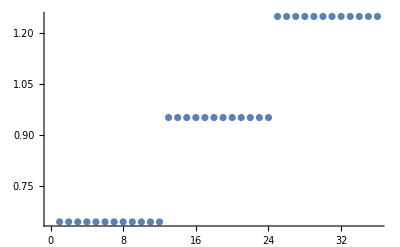

```mathematica
TraverseDiag2[plantri[[2]]]//Sort//ListPlot
```

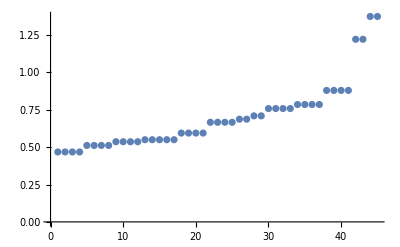

```mathematica
TraverseDiag2[plantri[[8]]]//Sort//ListPlot
```